## 用最短tour寻找最短超级排列

```mathematica
f[x_]/;x!=0:=x
dis[a_,b_]:=Block[{n=1,x,y},x=ToExpression@Characters[b];y=ToExpression@Characters[a];While[Take[x,n]!=Take[y,-n]&&n<len,n++];f[len-n]](*n个元素的全排列构成一个集合S，计算S中任意两个元素之间的距离，找到一个遍历所有元素的最短路线，就找到了一个最小超级排列*)
tourlen[t_]:=(dis@@@Partition[t,2,1]//Total)+len
```

#### 长度为3

```mathematica
len=3;
f[0]=len;
```

```mathematica
per=StringJoin/@Permutations[ToString/@Range[len]];
{slen,tour}=FindShortestTour[per,DistanceFunction->dis,Method->"Greedy"]
st=Drop[per[[tour]],-1]
s1={"123","231","312","213","132","321"}(*len=3的真正的最优解*)
```

{8,{1,6,3,2,4,5,1}}

{123,321,213,132,231,312}

{123,231,312,213,132,321}

```mathematica
st
```

{123,321,213,132,231,312}

```mathematica
tourlen/@{per,st,s1}
```

{15,10,9}

```mathematica
dm=Table[dis[per[[i]],per[[j]]],{i,len!},{j,len!}];
```

```mathematica
Thread[Rule@@@Partition[per[[tour]],2,1]->
dis@@@Partition[per[[tour]],2,1]]//Column
```

(123→321)→2
(321→213)→1
(213→132)→1
(132→231)→2
(231→312)→1
(312→123)→1

{1,6,3,2,4,5,1}

{1,4,5,3,2,6,1}

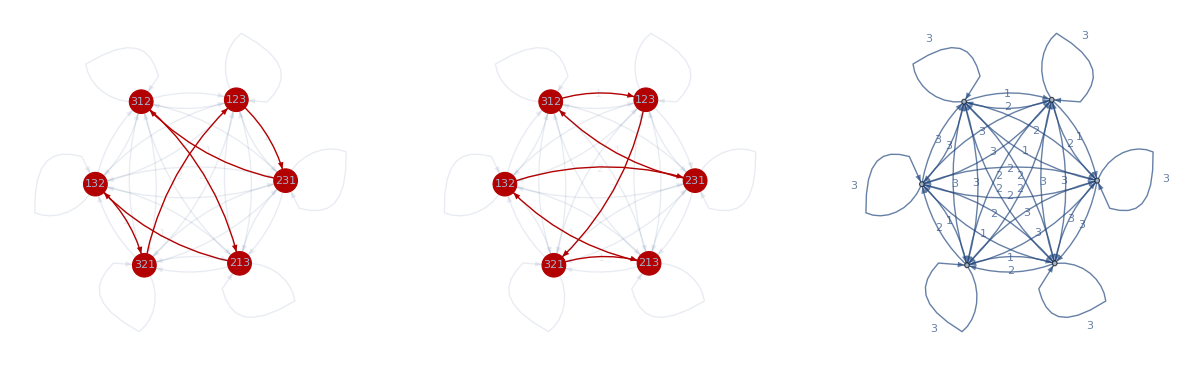

```mathematica
tour
stour3=Flatten@(Position[per,#]&/@(s1~Join~{"123"}))
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]],VertexSize-> .25,VertexLabels->Table[stour3[[i]]->Placed[per[[stour3]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[stour3,2,1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]]]],
HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .25,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

#### 长度为4

```mathematica
len=6
f[0]=len;
```

6

```mathematica
per=StringJoin/@Permutations[ToString/@Range[len]];
```

```mathematica
{slen,tour}=FindShortestTour[per,DistanceFunction->dis,Method->"SpaceFillingCurve"]
st=per[[Drop[%[[2]],-1]]]
```

{2519,{1,601,154,697,481,2,577,156,619,73,677,373,74,461,538,275,188,322,611,37,676,369,38,460,521,187,529,709,242,12,313,667,484,11,589,10,337,547,9,604,184,607,25,699,487,26,579,276,191,253,653,76,341,428,520,179,483,698,8,305,180,578,7,603,178,620,75,686,411,254,78,291,662,374,77,470,522,189,621,79,678,375,80,462,216,326,636,159,602,3,673,162,361,4,457,571,6,362,553,715,5,482,691,433,665,301,634,153,701,493,50,581,49,613,394,161,623,85,654,255,86,342,395,562,164,442,617,61,652,249,62,340,515,163,64,129,628,63,618,448,221,404,544,299,622,81,629,133,82,680,387,134,84,171,638,376,83,464,546,309,138,96,268,600,415,687,528,231,94,137,388,663,295,714,543,296,594,390,143,118,174,272,537,712,271,657,172,345,550,173,518,670,321,382,107,389,560,672,327,612,39,626,123,40,218,403,563,328,587,356,208,650,243,16,338,427,569,606,15,353,210,685,409,244,18,289,661,364,17,469,575,246,410,565,719,245,530,695,445,642,183,501,103,558,381,104,438,288,239,368,555,716,367,675,28,459,572,30,435,692,488,29,596,27,608,280,209,349,551,366,23,290,541,713,24,421,689,314,473,508,131,70,511,705,146,585,252,71,199,645,69,498,472,194,397,683,492,45,506,125,46,559,717,386,126,48,170,517,707,169,637,334,370,41,385,679,124,42,463,573,47,372,358,439,693,360,120,144,270,416,567,720,269,536,696,447,142,114,149,512,694,441,150,598,392,561,718,391,681,148,465,574,264,119,588,176,519,708,175,639,412,257,92,292,633,151,706,513,152,586,294,116,263,414,115,383,660,279,206,348,205,647,359,22,599,21,486,232,593,20,434,19,485,226,590,51,614,400,203,380,101,446,591,480,141,510,112,320,423,690,509,139,106,440,666,303,140,108,399,684,200,468,262,113,207,648,261,534,110,318,109,503,396,167,595,168,475,166,451,165,516,350,202,330,597,357,432,584,431,355,192,331,425,525,223,564,405,224,444,258,95,471,576,117,384,592,378,93,351,552,111,504,286,233,502,105,454,649,186,241,185,274,452,285,540,230,324,229,527,354,477,312,467,352,453,336,443,306,407,235,479,240,476,282,215,455,238,449,237,408,91,377,526,225,332,234,329,228,325,671,554,365,227,406,316,68,251,532,67,497,466,158,393,682,157,635,315,668,494,53,710,531,248,54,548,339,52,247,651,401,211,298,212,281,418,615,55,582,56,702,495,420,287,236,300,580,32,489,700,31,609,297,664,398,197,688,417,278,198,430,347,196,277,659,195,644,496,59,704,507,128,60,524,219,58,127,627,426,333,57,616,424,323,220,539,283,65,250,631,145,66,130,655,265,711,535,266,132,72,478,549,343,570,429,344,450,89,256,632,147,90,136,267,656,88,135,630,87,624,568,419,284,222,304,610,33,523,217,34,625,121,583,35,490,310,643,193,36,122,703,505,311,214,307,545,458,14,363,204,674,13,605,201,646,542,293,102,260,413,566,99,500,177,640,422,317,100,533,259,181,641,436,44,371,556,43,491,346,182,273,658,437,98,379,557,97,499,155,514,308,213,402,669,319,474,456,160,302,190,335,1}}

{123456,612345,234561,651234,512346,123465,561234,234651,615234,152346,641523,415236,152364,461523,532461,324615,246153,352461,613524,135246,641352,413526,135264,461352,524613,246135,531246,653124,312465,124653,351246,635124,512463,124635,563124,124563,361245,536124,124536,612453,245361,613245,132456,651324,513246,132465,561324,324651,246513,315246,631524,152463,361524,436152,524361,243615,512436,651243,124365,345612,243651,561243,124356,612435,243561,615243,152436,643152,431526,315264,152643,341526,634152,415263,152634,463152,524631,246315,615324,153246,641532,415326,153264,461532,256431,354162,623541,235416,612354,123546,641235,235641,412356,123564,461235,546123,123654,412365,541236,654123,123645,512364,645123,451236,634512,345126,623451,234516,651423,514236,142365,561423,142356,614235,423561,235614,615423,154236,631542,315426,154263,361542,423615,542361,236154,452361,614523,145236,631452,314526,145263,361452,523614,236145,145362,214536,621453,145326,614532,453261,261534,426153,534261,342615,615342,153426,621534,215346,153462,642153,421536,215364,153642,241536,624153,415362,153624,462153,534621,346215,215643,156432,321564,564321,432156,643215,526431,264315,156342,215634,421563,634215,342156,653421,534216,342165,563421,421653,216534,165342,241653,324165,532416,653241,324156,632415,241563,362415,536241,241635,524163,635241,352416,416352,163524,421635,542163,635421,354216,613542,135426,621354,213546,135462,261354,426135,542613,354261,562413,365142,254361,631254,312546,125463,361254,436125,543612,612543,125436,364512,254631,643125,431256,312564,125643,341256,634125,412563,125634,463125,546312,312654,431265,543126,654312,312645,531264,645312,453126,624531,245316,516324,163245,541632,416325,163254,451632,326541,265413,413265,541326,654132,413256,641325,132564,461325,546132,132654,451326,645132,513264,132645,564132,132546,613254,325461,254613,364125,536412,412653,126534,341265,534126,653412,126543,435126,643512,351264,463512,521463,214635,146352,523146,652314,231465,562314,314652,146523,253146,625314,146325,514632,463251,251364,425136,642513,513642,136425,521364,213645,136452,542136,654213,421365,213654,136542,241365,524136,652413,241356,624135,356241,413562,135624,421356,642135,213564,135642,462135,546213,136524,413652,365241,452136,645213,365421,165432,216543,321654,432165,543216,654321,321645,532164,645321,453216,216453,164532,231645,523164,645231,452316,231654,564231,423165,542316,654231,423156,642315,231564,462315,546231,316542,165423,562431,243165,524316,652431,243156,624315,431562,315624,156243,341562,623415,234156,652341,523416,234165,562341,341652,165243,316524,431652,165234,416523,632541,325416,254163,362541,254136,625413,365412,126453,564312,126435,512643,264351,563412,126354,451263,126345,512634,263451,563142,142536,614253,425361,253614,416253,162534,453162,563214,465321,216435,521643,164352,352164,435216,643521,521634,216345,163452,452163,634521,345216,216354,163542,425316,642531,253164,462531,316452,164523,254316,625431,316425,531642,164253,351642,164235,516423,423651,236514,564123,236541,465123,236451,456123,236415,523641,364152,253461,354621,564213,365214,436521,562143,436512,365124,246531,356124,435612,526314,263145,542631,426315,263154,452631,315642,156423,463215,546321,165324,416532,563241,415632,156324,364215,536421,164325,516432,326451,264513,516342,163425,456231,631245,245631,312456,245613,324561,456132,326415,532641,264153,352641,264135,526413,364521,465213,346521,462513,364251,456213,356421,452613,345621,426513,265134,465312,265431,465132,325641,256413,456312,265341,453612,265314,426531,156234,415623,526341,263415,356142,264531,354612,263541,354126,635412,541263,412635,263514,426351,351462,146253,314625,531462,146235,514623,462351,235164,423516,642351,235146,623514,351426,635142,514263,142635,653142,531426,314265,142653,536142,361425,142563,314256,631425,425613,256134,342561,256143,325614,432561,614325,143256,561432,143265,651432,514326,432651,326514,265143,342651,561342,134265,513426,651342,134256,613425,342516,634251,425163,251634,643251,432516,325164,251643,436251,362514,251463,325146,632514,251436,625143,514362,143625,652143,521436,214365,143652,526143,261435,143562,214356,621435,435621,356214,143526,614352,435261,352614,261453,532614,326145,145623,314562,623145,231456,145632,214563,632145,321456,653214,532146,321465,214653,146532,465231,536214,362145,543621,436215,362154,453621,154623,315462,623154,231546,154632,215463,321546,632154,154362,215436,621543,154326,615432,543261,432615,326154,261543,345261,613452,134526,526134,261345,134562,621345,213456,562134,134625,513462,346251,625134,251346,134652,213465,652134,521346,346512,256341,346125,534612,461253,125364,412536,253641,641253,125346,612534,253416,625341,534162,341625,162543,316254,431625,543162,162435,516243,243516,624351,435162,351624,162453,531624,316245,245136,624513,451362,136254,413625,541362,136245,513624,362451,245163,324516,632451,451623,162354,416235,541623,162345,516234,234615,523461,346152,256314,425631,635214,352146,463521,456321,235461,345162,246351,356412}

```mathematica
tourlen/@{per,st}
```

{93,55}

```mathematica
dm=Table[dis[per[[i]],per[[j]]],{i,len!},{j,len!}];
```

```mathematica
Thread[Rule@@@Partition[per[[tour]],2,1]->
dis@@@Partition[per[[tour]],2,1]]//Column
```

(1234→3421)→2
(3421→1342)→3
(1342→4213)→2
(4213→3142)→3
(3142→2314)→3
(2314→1423)→2
(1423→4231)→1
(4231→3214)→4
(3214→1432)→2
(1432→4321)→1
(4321→2143)→2
(2143→4312)→2
(4312→1243)→2
(1243→2431)→1
(2431→3124)→2
(3124→2134)→4
(2134→3412)→2
(3412→4123)→1
(4123→3241)→3
(3241→1324)→3
(1324→2413)→2
(2413→4132)→1
(4132→2341)→3
(2341→1234)→3

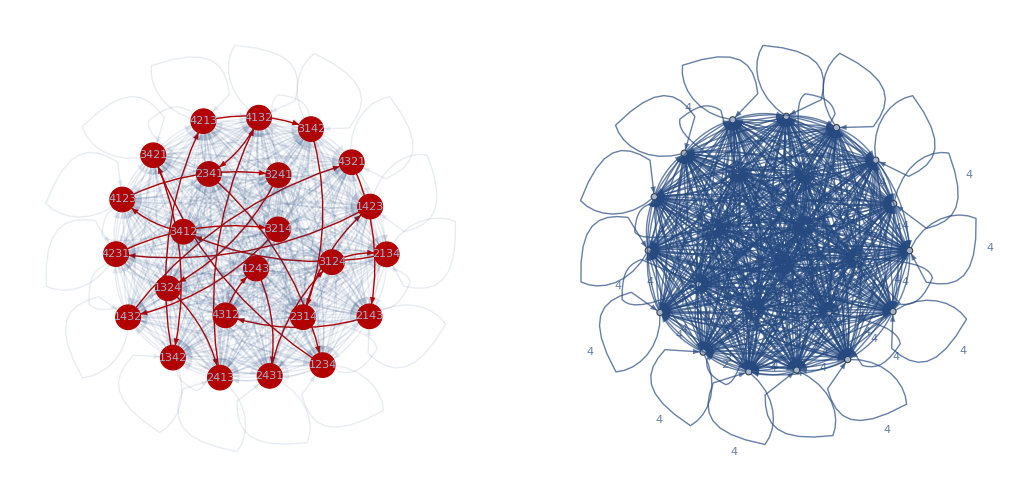

```mathematica
{slen,tour}=FindShortestTour[Range[len!],DistanceFunction->(dm[[#1,#2]]&)];(*等价写法*)
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .55,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

## 内置算法找不到最短的路径

### 4阶

{15,{1,2,3,4,1}}

{15,{1,2,3,4,1}}

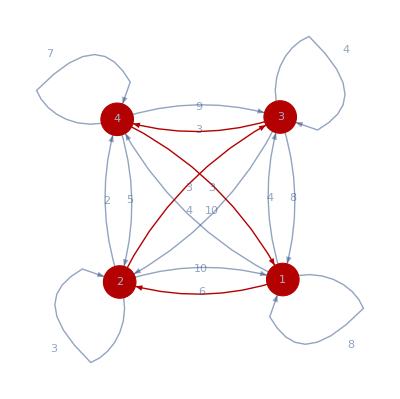

-Graphics-

```mathematica
d=RandomInteger[{1,10},{4,4}];
{len,tour}=FindShortestTour[{1,2,3,4},DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[3]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 5阶

{20,{1,5,4,2,3,1}}

{20,{1,5,4,2,3,1}}

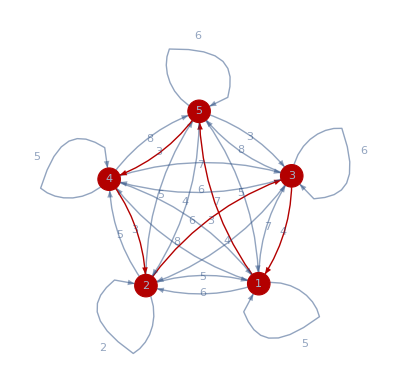

-Graphics-

```mathematica
n=5;d=RandomInteger[{1,8},{n,n}];
{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 6阶

{21,{1,3,4,5,6,2,1}}

{7,{1,5,2,6,4,3,1}}

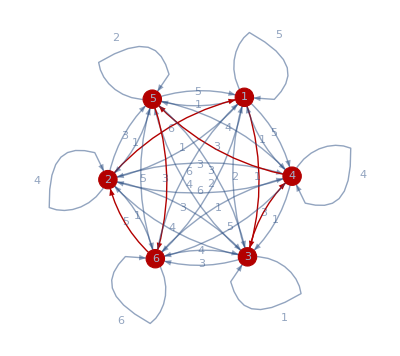

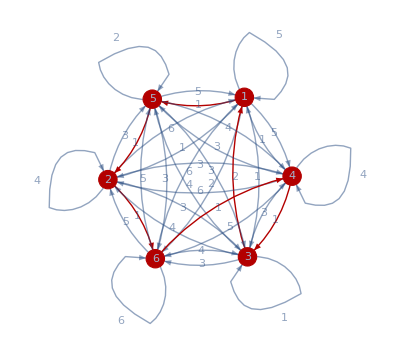

```mathematica
n=6;d=RandomInteger[{1,6},{n,n}];{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 7阶

{197,{1,6,2,7,3,5,4,1}}

{197,{1,6,2,7,3,5,4,1}}

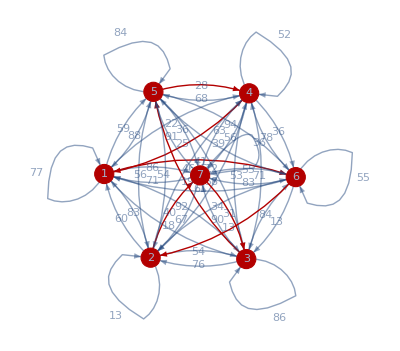

-Graphics-

```mathematica
n=7;d=RandomInteger[{1,100},{n,n}];{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&),Method->"AllTours"]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 8阶

{259,{1,3,4,5,7,2,8,6,1}}

{177,{1,6,7,2,8,3,5,4,1}}

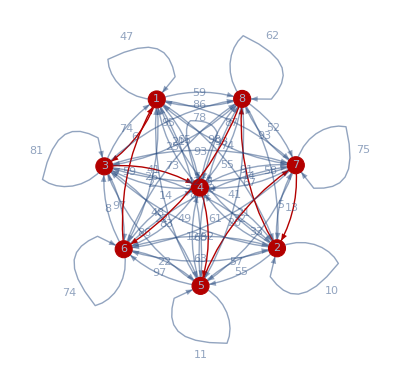

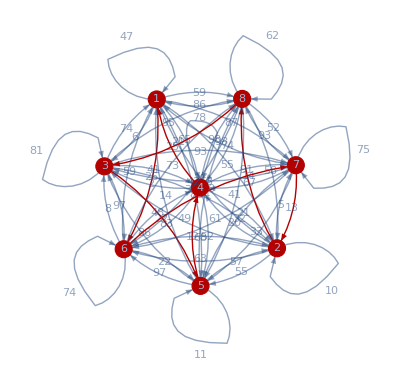

```mathematica
n=8;d=RandomInteger[{1,100},{n,n}];{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 24阶

{836,{1,24,12,13,6,20,10,8,14,23,4,17,7,21,15,22,18,9,3,5,16,2,19,11,1}}

Permutations::fac: In Permutations[{1,2,3,4,5,6,7,8,9,10,«13»}] there are at least 21 distinct elements in the input list, and the requested permutation lengths include one that is at least 21. The result cannot be computed because it has length at least 21 factorial, which is not a machine integer.

Join::heads: Heads List and Permutations at positions 1 and 2 are expected to be the same.

Part::pkspec1: The expression Permutations[{1,2,3,4,5,6,7,8,9,10,«13»}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{Total[1+{{49,64,46,90,5,93,64,79,97,40,2,59,31,63,43,89,1,29,43,43,89,80,86,3},{81,11,52,80,41,72,26,62,53,96,65,80,82,92,86,6,85,95,26,67,34,66,94,87},{43,61,50,87,10,3,89,78,5,80,93,33,68,26,97,11,26,14,51,70,85,52,99,94},{39,57,66,87,70,81,24,95,52,91,78,52,70,55,31,7,11,100,86,45,16,89,11,61},{69,35,44,62,8,95,37,58,40,33,36,31,46,54,59,3,14,80,37,100,77,83,16,92},{87,16,42,18,39,38,69,31,87,32,92,19,15,54,25,6,71,94,68,8,49,56,28,11},{5,28,5,76,75,24,36,65,79,23,100,79,39,42,51,17,9,96,52,99,1,71,71,60},{56,1,85,53,25,7,62,97,50,15,57,93,33,10,76,37,93,71,90,67,70,92,99,42},{69,40,32,67,92,82,1,1,41,57,11,7,68,26,36,87,53,5,52,35,47,38,33,66},{78,29,64,8,38,98,71,72,4,58,35,89,86,53,71,58,27,72,98,5,53,3,10,45},{79,1,18,47,3,43,79,9,77,82,84,64,64,64,31,89,52,37,19,16,90,73,15,89},{98,47,60,10,91,26,65,78,22,49,84,6,18,97,11,12,12,93,43,58,36,2,79,8},{14,86,42,60,67,67,28,67,8,55,28,36,81,81,62,73,21,45,87,31,57,71,51,82},{3,79,4,29,64,1,62,83,83,42,67,65,27,49,79,69,62,94,37,24,57,37,28,35},{34,98,27,74,20,43,50,21,1,72,39,24,42,33,28,60,50,95,67,50,2,1,76,34},{10,53,41,70,66,59,12,88,5,75,17,4,47,54,54,66,28,68,12,34,23,13,32,55},{64,13,81,87,19,63,41,47,26,1,8,82,54,47,83,98,93,62,54,47,60,33,43,88},{81,81,46,57,5,69,28,88,26,52,77,90,22,57,63,3,29,79,87,47,90,4,85,59},{8,32,95,56,36,35,25,71,92,43,21,30,50,72,62,85,74,72,85,35,20,85,81,19},{21,47,97,99,21,10,4,19,48,57,58,68,78,3,1,93,5,18,28,88,60,90,52,24},{89,74,56,85,51,23,27,69,14,29,14,37,9,96,31,31,58,59,36,51,49,84,17,26},{48,2,95,52,19,30,36,6,78,69,85,24,83,93,32,39,63,75,58,6,61,7,65,34},{71,26,4,98,58,97,23,87,12,13,47,30,100,35,81,73,27,10,94,88,92,48,55,80},{14,84,21,38,85,10,62,4,63,5,86,65,97,44,58,14,71,40,60,6,71,11,9,50}}⟦{1},Permutations[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}]⟧],1+Join[{1},Permutations[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}],{1}]}

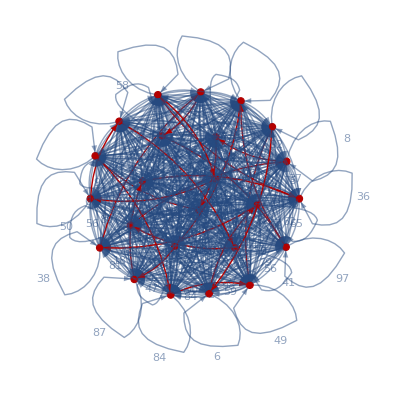

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

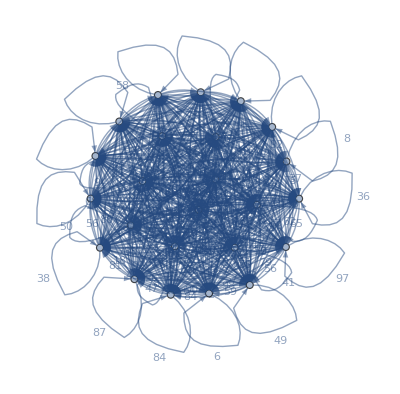

```mathematica
n=24;d=RandomInteger[{1,100},{n,n}];{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

## 草稿

```mathematica
FindShortestTour
```

```mathematica
Graph
```

```mathematica
f[x_]:=x/.{y__,z_,z_,w__}:>{y,z,w}
```

```mathematica
f[Flatten/@(Permutations@Permutations[{1,2,3}])][[1;;10]]
```

{{1,2,3,1,3,2,1,3,2,3,1,3,1,2,3,2,1},{1,2,3,1,3,2,1,3,2,3,1,3,2,1,3,1,2},{1,2,3,1,3,2,1,3,3,1,2,2,3,1,3,2,1},{1,2,3,1,3,2,1,3,3,1,2,3,2,1,2,3,1},{1,2,3,1,3,2,1,3,3,2,1,2,3,1,3,1,2},{1,2,3,1,3,2,1,3,3,2,1,3,1,2,2,3,1},{1,2,3,1,3,2,3,1,2,1,3,3,1,2,3,2,1},{1,2,3,1,3,2,3,1,2,1,3,3,2,1,3,1,2},{1,2,3,1,3,2,3,1,3,1,2,2,1,3,3,2,1},{1,2,3,1,3,2,3,1,3,1,2,3,2,1,2,1,3}}

```mathematica
a={3,4,2,1};
b={1,2,3,4};
```

```mathematica
a={3,4,2,1};
b={4,3,2,1};
```

```mathematica
n=1;While[Take[a,n]!=Take[b,-n],n++]
```

```mathematica
n
```

4

```mathematica
Take[a,2]
```

{1,2}

```mathematica
k
```

```mathematica
Table[{Take[a,n],Take[b,-n]},{n,0,4}]
```

{{{},{}},{{3},{1}},{{3,4},{2,1}},{{3,4,2},{3,2,1}},{{3,4,2,1},{4,3,2,1}}}

```mathematica
Table[{Take[a,n]!=Take[b,-n]},{n,1,4}]
```

{{True},{True},{True},{True}}

```mathematica
Block
```

```mathematica
ToString/@Range[len]
```

{1,2,3,4,5}

```mathematica
dis["12345","45213"]
```

3

```mathematica
dis@@@Partition[s1]
```

```mathematica
dis
```

```mathematica
MapThread
```

```mathematica
Thread
```

```mathematica
Map
```

```mathematica
dis[st[[1]],st[[2]]]
```

1

```mathematica
shortestlist=per[[(%255)[[2]]]];
```

```mathematica
(%255)[[2]]//Length
```

721

```mathematica
n
```

4

```mathematica
ToString
```

```mathematica
ToExpression@Characters["1234"]
```

{1,2,3,4}

```mathematica
dis[a_,b_]:=Block[{n=1,x,y},While[Take[a,n]!=Take[b,-n]&&n<len,n++];n]
```

```mathematica
ToExpression[Characters@"1243"]
```

{1,2,4,3}

```mathematica
dis[{1,2,3,4},{1,2,4,3}]
```

ToExpression::notstrbox: Characters[1] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: Characters[2] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: Characters[3] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

1

```mathematica
dis["1234","2341"]
```

1

```mathematica
Table[dis[per[[i]],per[[i+1]]],{i,1,3!-1}]//Total
```

12

```mathematica
dis["1234","3421"]
```

3

```mathematica
n
```

4

```mathematica
dis[b,a]
```

4

```mathematica
n
```

5

```mathematica
d=SparseArray[{{1,2}->1,{2,1}->1,{6,1}->1,{6,2}->1,{5,1}->1,{1,5}->1,{2,6}->1,{2,3}->10,{3,2}->10,{3,5}->1,{5,3}->1,{3,4}->1,{4,3}->1,{4,5}->15,{4,1}->1,{5,4}->15,{5,2}->1,{1,4}->1,{2,5}->1,{1,6}->1},{6,6},Infinity];
```

```mathematica
d//MatrixForm
```

(∞ | 1 | ∞ | 1 | 1 | 1
1 | ∞ | 10 | ∞ | 1 | 1
∞ | 10 | ∞ | 1 | 1 | ∞
1 | ∞ | 1 | ∞ | 15 | ∞
1 | 1 | 1 | 15 | ∞ | ∞
1 | 1 | ∞ | ∞ | ∞ | ∞)

```mathematica
{len,tour}=FindShortestTour[{1,2,3,4,5,6},DistanceFunction->(dm[[#1,#2]]&)]
```

{12,{1,6,2,3,5,4,1}}

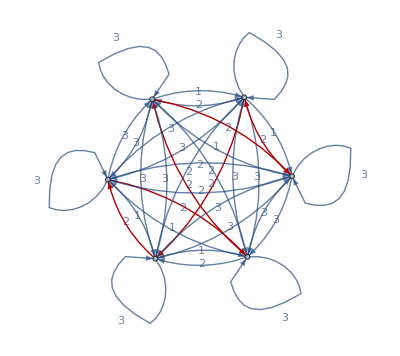

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
HighlightGraph[WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"],{1->6,6->2,2->3,3->5,5->4,4->1}]
```

```mathematica
dm=Table[dis[per[[i]],per[[j]]],{i,len!},{j,len!}];
```

```mathematica
dm//MatrixForm
```

(4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 2 | 2
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 1 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 2 | 2 | 4 | 4
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 1 | 4 | 4
4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1
4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 2 | 2
4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 2 | 2 | 4 | 4 | 4 | 4
4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 1 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4
4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 1 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4
4 | 4 | 4 | 4 | 2 | 2 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4
2 | 2 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4
1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
4 | 4 | 1 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
4 | 4 | 2 | 2 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 1 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4)

```mathematica
FindShortestTour[Range[len!],DistanceFunction->(dm[[#1,#2]]&)]
st=per[[Drop[%[[2]],-1]]](*一种等效的写法*)
```

{54,{1,18,4,21,14,9,5,22,15,6,24,8,23,2,12,13,7,17,19,16,3,11,20,10,1}}

{1234,3421,1342,4213,3142,2314,1423,4231,3214,1432,4321,2143,4312,1243,2431,3124,2134,3412,4123,3241,1324,2413,4132,2341}

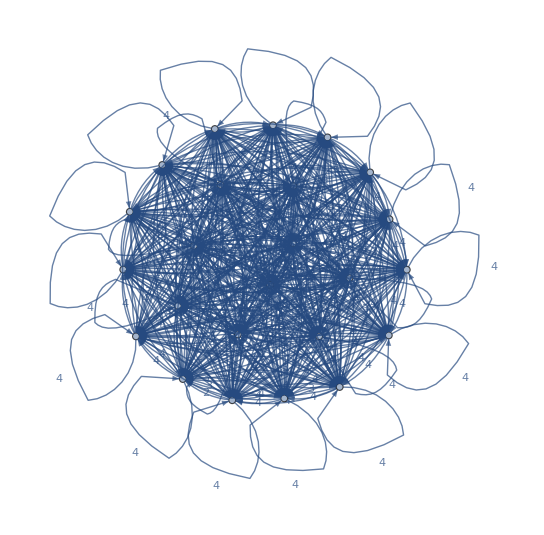

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight",VertexLabels->"Name"]
```

{105,{1,6,2,5,3,4,1}}

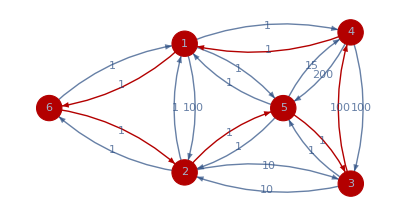

```mathematica
d=SparseArray[{{1,2}->100,{2,1}->1,{6,1}->1,{6,2}->1,{5,1}->1,{1,5}->1,{2,6}->1,{2,3}->10,{3,2}->10,{3,5}->1,{5,3}->1,{3,4}->100,{4,3}->100,{4,5}->200,{4,1}->1,{5,4}->15,{5,2}->1,{1,4}->1,{2,5}->1,{1,6}->1},{6,6},Infinity];{len,tour}=FindShortestTour[{1,2,3,4,5,6},DistanceFunction->(d[[#1,#2]]&)]
HighlightGraph[WeightedAdjacencyGraph[d,EdgeLabels->"EdgeWeight",VertexSize-> .25,VertexLabels->Placed[Automatic,Center]],Graph[Rule@@@Partition[tour,2,1]]]
```

```mathematica
Partition[per[[tour]],2,1]
```

{{1234,3421},{3421,1342},{1342,4213},{4213,3142},{3142,2314},{2314,1423},{1423,4231},{4231,3214},{3214,1432},{1432,4321},{4321,2143},{2143,4312},{4312,1243},{1243,2431},{2431,3124},{3124,2134},{2134,3412},{3412,4123},{4123,3241},{3241,1324},{1324,2413},{2413,4132},{4132,2341},{2341,1234}}

```mathematica
dis@@@Partition[per[[tour]],2,1]
```

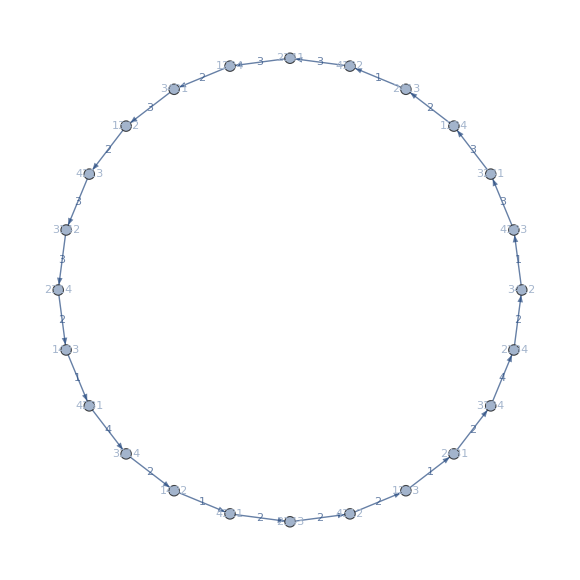

```mathematica
Graph[Rule@@@Partition[per[[tour]],2,1],EdgeLabels->Thread[Rule@@@Partition[per[[tour]],2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexLabels->Placed["Name",Center]]
```

```mathematica
Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]
```

{1→Placed[1234,Center],18→Placed[3421,Center],4→Placed[1342,Center],21→Placed[4213,Center],14→Placed[3142,Center],9→Placed[2314,Center],5→Placed[1423,Center],22→Placed[4231,Center],15→Placed[3214,Center],6→Placed[1432,Center],24→Placed[4321,Center],8→Placed[2143,Center],23→Placed[4312,Center],2→Placed[1243,Center],12→Placed[2431,Center],13→Placed[3124,Center],7→Placed[2134,Center],17→Placed[3412,Center],19→Placed[4123,Center],16→Placed[3241,Center],3→Placed[1324,Center],11→Placed[2413,Center],20→Placed[4132,Center],10→Placed[2341,Center]}

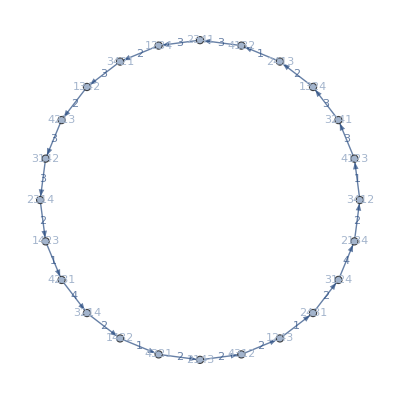

```mathematica
Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]]
```

{54,{1,18,4,21,14,9,5,22,15,6,24,8,23,2,12,13,7,17,19,16,3,11,20,10,1}}

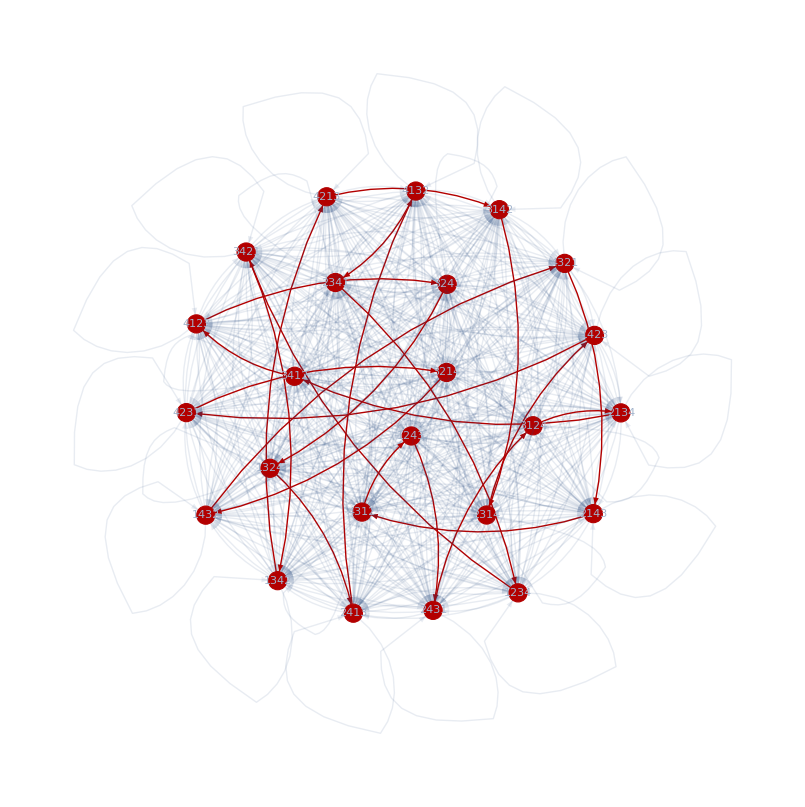

```mathematica
WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]
```

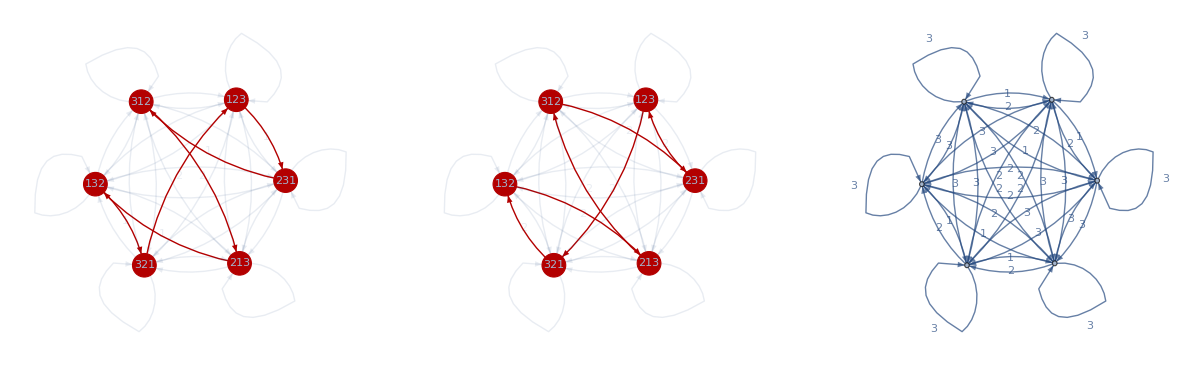

```mathematica
stour3=Flatten@(Position[per,#]&/@(s1~Join~{"123"}))
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]],VertexSize-> .25,VertexLabels->Table[stour3[[i]]->Placed[per[[stour3]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[stour3,2,1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]]]],
HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .25,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

```mathematica
s1~Join~{"123"}
```

{123,231,312,213,132,321,123}

{1,4,5,3,2,6,1}

```mathematica
tour
```

{1,6,2,3,5,4,1}

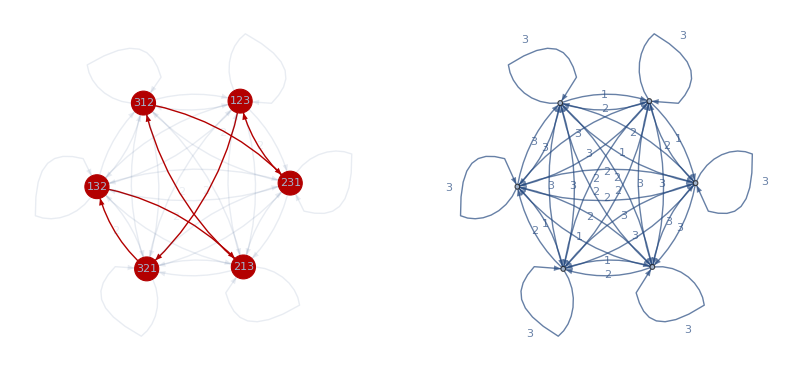

```mathematica
{slen,tour}=FindShortestTour[Range[len!],DistanceFunction->(dm[[#1,#2]]&)];(*等价写法*)
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .25,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

```mathematica
d=RandomInteger[{1,10},{6,6}];
```

{30,{1,6,5,2,4,3,1}}

{12,{1,3,2,5,6,4,1}}

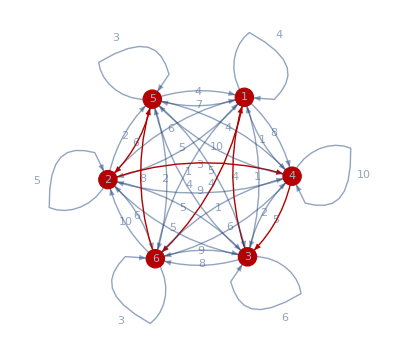

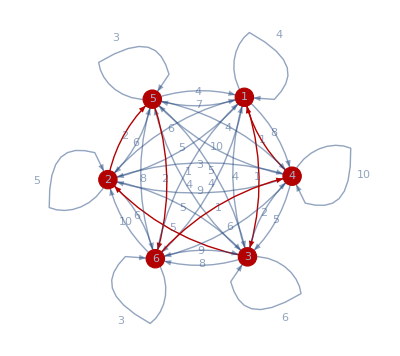

```mathematica
{len,tour}=FindShortestTour[{1,2,3,4,5,6},DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[5]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

```mathematica
d[[#1,#2]]&@@@Partition[{1,3,2,5,6,4,1},2,1]
```

{1,5,2,2,1,1}

```mathematica
Total[%]
```

12

```mathematica
{4,9,5,2,4,1}
```

{4,9,5,2,4,1}

```mathematica
{{5,5,2,10,2,1},{5,5,2,6,8,4},{5,5,4,4,6,1},{5,5,4,2,1,1},{5,5,8,1,10,4},{5,5,8,8,4,1},{5,3,5,4,2,1},{5,3,5,8,8,4},{5,3,10,5,8,1},{5,3,10,2,9,4},{5,3,6,9,4,4},{5,3,6,8,5,4},{5,2,5,2,6,1},{5,2,5,8,1,1},{5,2,4,5,8,1},{5,2,4,6,9,4},{5,2,2,9,2,1},{5,2,2,1,5,4},{5,6,9,2,10,4},{5,6,9,4,4,1},{5,6,1,5,4,4},{5,6,1,10,5,4},{5,6,8,5,2,1},{5,6,8,4,5,4},{1,5,3,10,2,1},{1,5,3,6,8,4},{1,5,2,4,6,1},{1,5,2,2,1,1},{1,5,6,1,10,4},{1,5,6,8,4,1},{1,2,9,2,2,1},{1,2,9,6,8,4},{1,2,10,6,6,1},{1,2,10,2,10,6},{1,2,6,10,2,4},{1,2,6,8,6,6},{1,4,6,3,6,1},{1,4,6,6,1,1},{1,4,4,9,6,1},{1,4,4,6,10,6},{1,4,2,10,3,1},{1,4,2,1,9,6},{1,8,10,3,10,4},{1,8,10,2,4,1},{1,8,1,9,2,4},{1,8,1,10,6,6},{1,8,8,6,3,1},{1,8,8,4,9,6},{8,9,5,4,2,1},{8,9,5,8,8,4},{8,9,2,5,8,1},{8,9,2,2,9,4},{8,9,6,9,4,4},{8,9,6,8,5,4},{8,5,5,2,2,1},{8,5,5,6,8,4},{8,5,4,6,6,1},{8,5,4,2,10,6},{8,5,8,10,2,4},{8,5,8,8,6,6},{8,10,6,5,8,1},{8,10,6,6,9,4},{8,10,5,5,6,1},{8,10,5,8,10,6},{8,10,2,10,5,4},{8,10,2,9,5,6},{8,6,10,5,4,4},{8,6,10,2,5,4},{8,6,9,5,2,4},{8,6,9,4,6,6},{8,6,8,6,5,4},{8,6,8,5,5,6},{7,6,5,2,6,1},{7,6,5,8,1,1},{7,6,3,5,8,1},{7,6,3,6,9,4},{7,6,6,9,2,1},{7,6,6,1,5,4},{7,5,5,3,6,1},{7,5,5,6,1,1},{7,5,2,9,6,1},{7,5,2,6,10,6},{7,5,8,10,3,1},{7,5,8,1,9,6},{7,4,9,5,8,1},{7,4,9,6,9,4},{7,4,5,5,6,1},{7,4,5,8,10,6},{7,4,6,10,5,4},{7,4,6,9,5,6},{7,2,10,5,2,1},{7,2,10,3,5,4},{7,2,9,5,3,1},{7,2,9,2,9,6},{7,2,1,9,5,4},{7,2,1,5,5,6},{4,10,5,2,10,4},{4,10,5,4,4,1},{4,10,3,5,4,4},{4,10,3,10,5,4},{4,10,2,5,2,1},{4,10,2,4,5,4},{4,9,5,3,10,4},{4,9,5,2,4,1},{4,9,2,9,2,4},{4,9,2,10,6,6},{4,9,4,6,3,1},{4,9,4,4,9,6},{4,1,9,5,4,4},{4,1,9,2,5,4},{4,1,5,5,2,4},{4,1,5,4,6,6},{4,1,10,6,5,4},{4,1,10,5,5,6},{4,8,6,5,2,1},{4,8,6,3,5,4},{4,8,5,5,3,1},{4,8,5,2,9,6},{4,8,4,9,5,4},{4,8,4,5,5,6}}[[104]]
```

{4,9,5,2,4,1}

```mathematica
d[[6,3]]
```

10

```mathematica
d[[#1,#2]]&@@@(exp[[1]])
```

{2,7,10,10,9,10}

```mathematica
Min[lengthlist]
```

22

```mathematica
Position[pathls,{1,2,3,5,6,4,1}]
```

{{4}}

```mathematica
Position[lengthlist,Min[lengthlist]]
```

{{104}}

```mathematica
pathls[[71]]
```

{1,4,6,5,2,3,1}